## Distribution

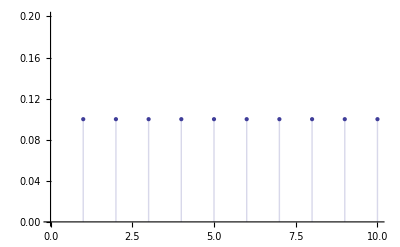

```mathematica
ListPlot[Table[PDF[DiscreteUniformDistribution[{1,10}],k],{k,1,10}],Filling->Axis]
```

```mathematica
PDF[BernoulliDistribution[p],k]
```

Piecewise[{{1-p, k==0}, {p, k==1}, {0, True}}]

```mathematica
PDF[BernoulliDistribution[p],k]
```

Piecewise[{{1-p, k==0}, {p, k==1}, {0, True}}]

```mathematica
Binomial[100,5]
```

75287520

```mathematica
PDF[BinomialDistribution[n,p],k]
```

(1-p)^(-k+n) p^k Binomial[n,k]

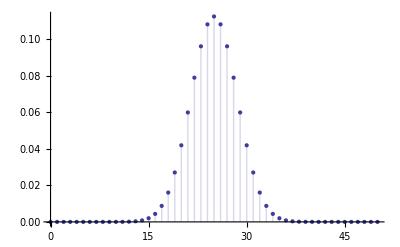

```mathematica
ListPlot[Table[{k,PDF[BinomialDistribution[50,0.5],k]},{k,0,50}],Filling->Axis]
```

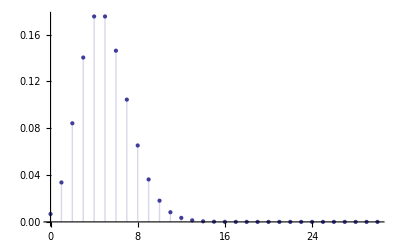

```mathematica
ListPlot[Table[{k,PDF[PoissonDistribution[5],k]},{k,0,30}],Filling->Axis]
```

```mathematica
PDF[NegativeBinomialDistribution[n,p],k]
```

(1-p)^k p^n Binomial[-1+k+n,-1+n]

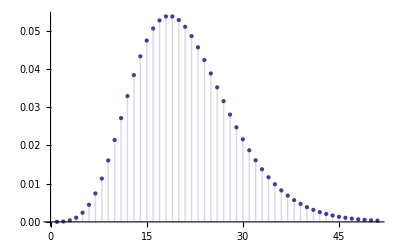

```mathematica
ListPlot[Table[PDF[NegativeBinomialDistribution[10,1/3],k],{k,0,50}],Filling->Axis]
```